# © Kamal K. Barley, Andreas Ruffing, and Sergei K. Suslov “Oganesson versus Uranium Hydrogen-like Ions from the Viewpoint of Old Quantum Mechanics”

arXiv:2509.06249v2[quant-ph] 11 Sept 2025

https://arxiv.org/pdf/2509.06249

(Last modified/executed on September  21, 2025;  4:50 AM Arizona time.)

```mathematica
SetDirectory[NotebookDirectory[]];
```

0.171738

0.989201

0.013287

{0.00014349,0.0264305}

30.3026

36.5858

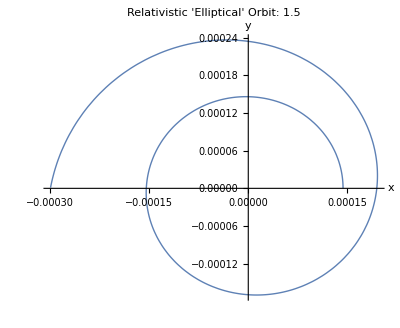

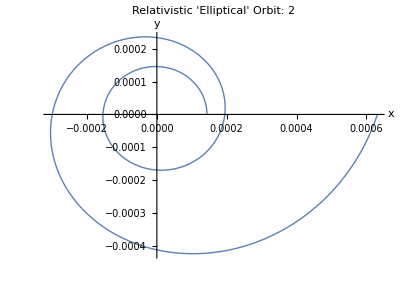

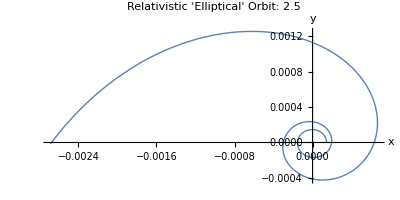

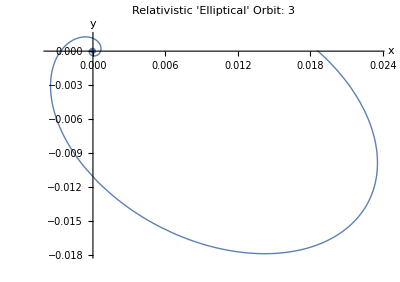

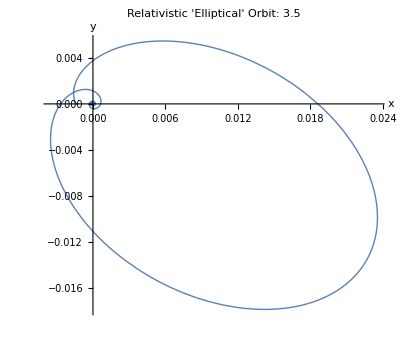

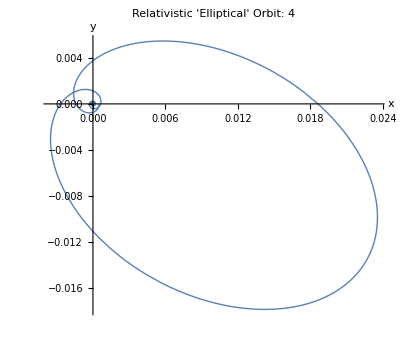

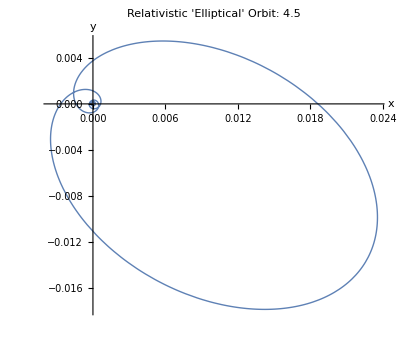

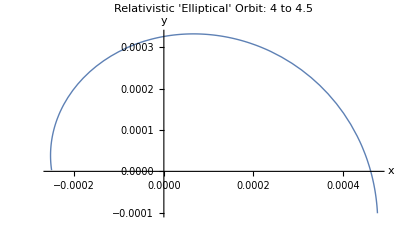

```mathematica
(*---Constants and Setup---*)(*Pretty print subscript-style variables for display only*)MakeBoxes[nt,StandardForm]:=SubscriptBox["n","t"]
MakeBoxes[nr,StandardForm]:=SubscriptBox["n","r"]

(*Physical constants*)
Z=135; (*Atomic number number 135 is assigned for a hypothetical undiscovered element temporarily named Untripentium, Utp*)

α=1/137.036; (*Fine structure constant*)

(*Quantum numbers*)
ntVal=1;
nrVal=1;

(*---Define symbolic formulas as functions---*)

(*Eq.(3.19)*)
ωFunc[nt_]:=Sqrt[nt^2-Z^2 α^2]/nt

(*Eq.(3.20)*)
ϵFunc[nt_,nr_]:=Sqrt[nr] Sqrt[(nr+2 Sqrt[nt^2-Z^2 α^2])]/(nr+Sqrt[nt^2-Z^2 α^2])

(*Eq.(3.21)*)
aFunc[nt_,nr_]:=((nr+Sqrt[nt^2-Z^2 α^2]) Sqrt[Z^2 α^2+(nr+Sqrt[nt^2-Z^2 α^2])^2])/Z

(*---Compute numeric values---*)

ωVal=ωFunc[ntVal]//N
ϵVal=ϵFunc[ntVal,nrVal]//N
aVal=aFunc[ntVal,nrVal]//N
{rMin=aVal*(1-ϵVal) //N, rMax=aVal*(1+ϵVal) //N}
DeltaTheta=2*Pi*((1/ωVal) -1) //N
PeriodTheta=2*Pi*(1/ωVal)  //N

(*---Define relativistic radial orbit r(t) from Eq.(3.9)---*)
r[t_]:=(aVal (1-ϵVal^2))/(1+ϵVal Cos[ωVal t])

 PolarPlot[r[t],{t,0,0.2575*PeriodTheta},PlotLabel->"Relativistic 'Elliptical' Orbit: 1.5",AxesLabel->{"x","y"},PlotRange->All,PlotStyle->Thick]
PolarPlot[r[t],{t,0,0.3435*PeriodTheta},PlotLabel->"Relativistic 'Elliptical' Orbit: 2",AxesLabel->{"x","y"},PlotRange->All,PlotStyle->Thick]
PolarPlot[r[t],{t,0,0.4295*PeriodTheta},PlotLabel->"Relativistic 'Elliptical' Orbit: 2.5",AxesLabel->{"x","y"},PlotRange->All,PlotStyle->Thick]
PolarPlot[r[t],{t,0,0.5153*PeriodTheta},PlotLabel->"Relativistic 'Elliptical' Orbit: 3",AxesLabel->{"x","y"},PlotRange->All,PlotStyle->Thick]
PolarPlot[r[t],{t,0,0.6025*PeriodTheta},PlotLabel->"Relativistic 'Elliptical' Orbit: 3.5",AxesLabel->{"x","y"},PlotRange->All,PlotStyle->Thick]
PolarPlot[r[t],{t,0,0.685*PeriodTheta},PlotLabel->"Relativistic 'Elliptical' Orbit: 4",AxesLabel->{"x","y"},PlotRange->All,PlotStyle->Thick]
PolarPlot[r[t],{t,0,0.7725*PeriodTheta},PlotLabel->"Relativistic 'Elliptical' Orbit: 4.5",AxesLabel->{"x","y"},PlotRange->All,PlotStyle->Thick]
PolarPlot[r[t],{t,0.68123*PeriodTheta, 0.7725*PeriodTheta},PlotLabel->"Relativistic 'Elliptical' Orbit: 4 to 4.5",AxesLabel->{"x","y"},PlotRange->All,PlotStyle->Thick]
PolarPlot[r[t],{t,0,0.8585*PeriodTheta},PlotLabel->"Relativistic 'Elliptical' Orbit: 5",AxesLabel->{"x","y"},PlotRange->All,PlotStyle->Thick]
PolarPlot[r[t],{t,0.7725*PeriodTheta,0.8585*PeriodTheta},PlotLabel->"Relativistic 'Elliptical' Orbit: 4.5 to 5",AxesLabel->{"x","y"},PlotRange->All,PlotStyle->Thick]
PolarPlot[r[t],{t,0,0.9*PeriodTheta},PlotLabel->"Relativistic 'Elliptical' Orbit: 5.5",AxesLabel->{"x","y"},PlotRange->All,PlotStyle->Thick]
PolarPlot[r[t],{t,0.8585*PeriodTheta,0.94447*PeriodTheta},PlotLabel->"Relativistic 'Elliptical' Orbit: 5 to 5.5",AxesLabel->{"x","y"},PlotRange->All,PlotStyle->Thick]
PolarPlot[r[t],{t,0,0.94447*PeriodTheta},PlotLabel->"Relativistic 'Elliptical' Orbit: 5.5",AxesLabel->{"x","y"},PlotRange->All,PlotStyle->Thick]
PolarPlot[r[t],{t,0.94447*PeriodTheta, 1.2022*PeriodTheta},PlotLabel->"Relativistic 'Elliptical' Orbit: 5.5 to 6",AxesLabel->{"x","y"},PlotRange->All,PlotStyle->Thick]
PolarPlot[r[t],{t,0, 1.2022*PeriodTheta},PlotLabel->"Relativistic 'Elliptical' Orbit: 6",AxesLabel->{"x","y"},PlotRange->All,PlotStyle->Thick]
PolarPlot[r[t],{t,0.94447*PeriodTheta, 1.288*PeriodTheta},PlotLabel->"Relativistic 'Elliptical' Orbit: 5.5 to 6.5",AxesLabel->{"x","y"},PlotRange->All,PlotStyle->Thick]
PolarPlot[r[t],{t,0, 1.29*PeriodTheta},PlotLabel->"Relativistic 'Elliptical' Orbit: 6.5",AxesLabel->{"x","y"},PlotRange->All,PlotStyle->Thick]
PolarPlot[r[t],{t,1.287*PeriodTheta, 1.547*PeriodTheta},PlotLabel->"Relativistic 'Elliptical' Orbit: 6.5 to 7",AxesLabel->{"x","y"},PlotRange->All,PlotStyle->Thick]
PolarPlot[r[t],{t,0, 1.547*PeriodTheta},PlotLabel->"Relativistic 'Elliptical' Orbit: 6 rotations",AxesLabel->{"x","y"},PlotRange->All,PlotStyle->Thick]
```

```mathematica
Export["UntripentiumIon134.pdf",]
```

UntripentiumIon134.pdf

```mathematica
(*Animation in Cartesian Coordinates*)Manipulate[ParametricPlot[{r[t] Cos[t],r[t] Sin[t]},{t,0,tMax},PlotStyle->{Blue,Thick},AxesLabel->{"x","y"},PlotLabel->Style["Relativistic Elliptical Orbit(Animated, Cartesian)",14,Bold],PlotRange->{{-rMax,rMax},{-rMax,rMax}},(*Fixed range ensures full visibility from Subscript[r, min] to Subscript[r, max]*)AspectRatio->1,PlotPoints->1000,PerformanceGoal->"Quality"],{tMax,0.01,24 Pi,Appearance->"Labeled"}]
```

Summary: 
In the above animation of the relativistic Kepler motion of an electron in a hypothetical hydrogen-like ion of Untripentium, Utp, when Z=135 and the nucleus is situated  in the fixed focus at the origin.  For this quantum state, we choose n_r=nr=1 and n_θ=nt=1 in the fine structure formula (3.18). By (3.19)-(3.21), one gets: ω= 0.171738,  ϵ=0.989201, and a=0.013287, in Bohr’s atomic units. The ‘winding number’ is 6.
The perihelion and aphelion move along two concentric circles around the nucleus with radii:   r_min=a (1-ϵ)=0.00014349 and r_max=a (1+ϵ)=0.0264305, respectively.  In the animation, the geometrical loci of the successive perihelia and aphelia, the outer and inner envelopes of the orbit, see Figure 3, are not shown for simplicity.
Rotation of the ellipse over one period is given by Δθ=2π(1/ω-1)=30.3026.